```mathematica
g=1.5;
κ=0.2;
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa0p2G1p5_N50000"];
PhiVSYKappa0p2G1p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa0p2G1p5[(π^(1/2)*Exp[(2 π*κ)^(1/2) x])/(1+Exp[(2 π*κ)^(1/2) x])];data=Table[{x,ϕss[x]},{x,-150,150,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x] +g^2;
L=200;
dx=.01;
total=200;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.63}];
(*dealing with mathematica being weird*)xRange=Range[-100,100,dx];
originalData=Table[{x,-fns[[1]]/. x->x},{x,xRange}];
ϕb=Interpolation[originalData];
```

InterpolatingFunction::dmval: Input value {1.66752×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.66939×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.67127×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

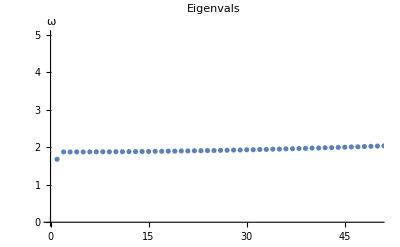

```mathematica
ListPlot[Sqrt[vals],PlotRange->{{0,50},{0,5}},AxesLabel->{"","ω"},PlotLabel->"Eigenvals"]
```

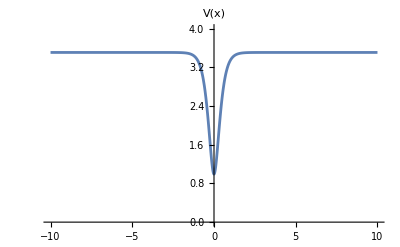

```mathematica
(*Plot[-fns[[1]],{x,-10,10},PlotRange->{{-10,10},{0,1.3}}]*)
Plot[potentialhamiltonian[x],{x,-10,10},PlotRange->{{-10,10},{0,4}},PlotLabel->"V(x)"]
```

```mathematica
ϕb[0]
ωb=Sqrt[vals[[1]]]
λ3=2*Pi^(3/2);
k2b=Sqrt[(2*ωb)^2-g^2-2*Pi*κ];
```

0.752301

1.67785

```mathematica
(*Testing to find k2b*)
2*ωb-Sqrt[vals[[177]]]
2*ωb-Sqrt[vals[[178]]]
```

0.00536769

-0.00797184

```mathematica
ϕk2b=(1/Sqrt[2])*(fns[[177+1]]+I*fns[[177]]);
Vbb2b=NIntegrate[Sin[2*Sqrt[Pi]*ϕss[x]]*ϕk2b*fns[[1]]*fns[[1]],{x,-100,100}]
Γ=λ3/(Sqrt[ωb]*k2b)*Vbb2b
```

-0.0283604-2.82093×10^-6 ⅈ

-0.0875644-8.70977×10^-6 ⅈ

```mathematica
Plot[{Cosh[Abs[Γ]*κ*t],Sinh[Abs[Γ]*κ*t]^2},{t,0,100},PlotLabels->{"|1b> initial state","|1k> initial state"},AxesLabel->{"t=τ/κ","<n_b(t)>"}]
```

-Graphics-

0.0840809

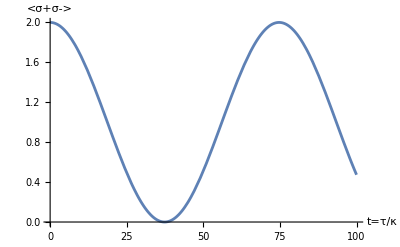

```mathematica
α=((Sqrt[2]*λ3^2)/ωb)*Abs[Vbb2b]^2
Plot[2*Cos[5*α*κ*t/2]^2,{t,0,100},AxesLabel->{"t=τ/κ","<σ+σ->"}]
```